## Function Definitions (Run this Chapter)

## Defining Functions (Run this Section)

### General Functions

```mathematica
(*The function below is used to swap the position of two elements in a list. The user inputs a list and the two indices of elements to be swapped. The function returns the inputted list with requested elements swapped.*)
Swap[list_,element1_,element2_]:= Module[{newlist},newlist = ReplacePart[list,{element1-> list[[element2]],element2-> list[[element1]]}];newlist];

NormKet[TestState_]:=((TestState[[FirstPosition[Flatten[Transpose[TestState]],_?(##≠ 0&)][[1]]]][[1]])^(-1))*TestState;

NormBra[TestState_]:=((TestState[[FirstPosition[TestState,_?(##≠ 0&)][[1]]]])^(-1))*TestState;

NormMatrix[matrix_]:=((Numerator[matrix[[Sequence@@FirstPosition[matrix,_?(##≠ 0&)]]]])^(-1))*matrix;

(*The function below is used to construct a modified density matrix corresponding to a permutation of qubits. The user inputs the dimension of the system along with an indexed list displaying the desired new ordering of qubits. The function will generate and return the desired change of basis matrix. *)
PermutedIdentity[dim_,NewOrderList_]:= Module[{OriginalList = Tuples[{0,1},dim],PermutedPiece,PermutedList={},NewIdentity = IdentityMatrix[2^dim],i,j,k},For[i=1,i< (2^dim) +1,i++,PermutedPiece = {};
For[k=1,k<Length[NewOrderList]+1,k++,AppendTo[PermutedPiece,OriginalList[[i]][[-NewOrderList[[-k]]]]]];AppendTo[PermutedList,PermutedPiece]];
If[Max[NewOrderList] ≤ dim,For[j=1 ,j<(2^dim) +1,j++,NewIdentity = Swap[NewIdentity,j,Position[PermutedList,OriginalList[[j]]][[1,1]]];PermutedList = Swap[PermutedList,j,Position[PermutedList,OriginalList[[j]]][[1,1]]]],Print["Invalid qubit number."],Print["Unable to interpret qubit number."]];
NewIdentity];

(*The GroupGenerate[] function generates a finite group of operators given a set of generators in a matrix representation. The option of parallel computation is offered by the second argument.*)
GroupGenerate[generators_,parallelQ_]:=Block[{g = Join[{IdentityMatrix[First[Dimensions[First[generators]]]]},generators],count=0,newElements=1},
count=Length[g];

If[parallelQ==True,
While[newElements>0,
g = DeleteDuplicates[Flatten[ParallelTable[g[[i]].g[[j]],{i,Length[g]},{j,Length[g]}],1]];
newElements = Length[g]-count;
count = Length[g];
],
While[newElements>0,
g = DeleteDuplicates[Flatten[Table[g[[i]].g[[j]],{i,Length[g]},{j,Length[g]}],1]];
newElements = Length[g]-count;
count = Length[g];
]];
g]

(*The NormedGroupGenerate[] function generates a version of the group with overall phase element removed.*)
NormedGroupGenerate[generators_,parallelQ_]:=Block[{g = Join[{IdentityMatrix[First[Dimensions[First[generators]]]]},generators],count=0,newElements=1},
count=Length[g];

If[parallelQ==True,
While[newElements>0,
g = DeleteDuplicates[Flatten[ParallelTable[NormKet[g[[i]].g[[j]]],{i,Length[g]},{j,Length[g]}],1]];
newElements = Length[g]-count;
count = Length[g];
],
While[newElements>0,
g = DeleteDuplicates[Flatten[Table[NormKet[g[[i]].g[[j]]],{i,Length[g]},{j,Length[g]}],1]];
newElements = Length[g]-count;
count = Length[g];
]];
g]
```

### Quantum Entropy Functions

#### Density Matrix and Projection

```mathematica
(*Here we define functions related to calculating entanglement entropy for quantum systems.*)
(*The function below builds the density matrix for a given quantum state by taking the outer product of the state ket with its corresponding bra. The user inputs the ket representing the chosen system and the function will return the corresponding density matrix.*)
DensityMatrix[state_]:= state.ConjugateTranspose[state];

(*The following function builds the state ket from a density matrix. The user inputs a density matrix describing a quantum state, and the function returns the ket representation of that state.*)
KetProjector[ρ_]:=Module[{stateket={},basisbra = {ConstantArray[0,Dimensions[ρ][[1]]]},indexlist = Range[Dimensions[ρ][[1]]],i,j},For[i=1,i<Length[indexlist]+1,i++,AppendTo[stateket,{Sqrt[Flatten[ReplacePart[basisbra,{1,i}-> 1].ρ.Transpose[ReplacePart[basisbra,{1,i}-> 1]]][[1]]]}]];stateket];

(*Here we use the code for computing partial trace from Mark S.Tame.The program is run by calling
TraceSystem[DensityMatrix,{SubsystemIndex1,SubsystemIndex2,...}].The first argument of the function is the original density matrix to be reduced.There is an assumed ordering of elements of your density matrix, consider the two-qubit example below:{{Basis, <00|, <01|, <10|, <11|}, {|00>, a, b, c, d}, {|01>, e, f, g, h}, {|10>, i, j, k, l}, {|11>, m, n, o, p}}                           
 Subscript[ρ, sys]=({{a, b, c, d}, {e, f, g, h}, {i, j, k, l}, {m, n, o, p}})Subsystem indexing follows that of the constituent qubits,beginning at index 1. For exampleTraceSystem[DensityMatrix,{1}]would return the reduced density matrix given by tracing out over the first qubit.*)


(*Program below. The user inputs the density matrix to be traced out, along with the indices of substates that will be traced over.*)
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= (

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]

]

;Return[TrkM])
```

#### Entanglement Entropy and Entropy Vector

```mathematica
(*Function to compute the reduced density matrix.*)
ReducedDensityMatrix[DM_,Subsystem_]:=Block[{totalDim =Log[2,First[Dimensions[DM]]],rangeDim =Range[Log[2,First[Dimensions[DM]]]],dimA=Length[Subsystem],dimB =Length[Complement[Subsystem]],order,dens,cons},
order = {Join[rangeDim[[-Subsystem]],Delete[rangeDim,-Transpose[{Subsystem}]]]};
dens = PermutedIdentity[totalDim,order].DM.ConjugateTranspose[PermutedIdentity[totalDim,order]];
Sum[KroneckerProduct[IdentityMatrix[2^dimA],Transpose[ReplacePart[cons,i->{1}]]].dens .KroneckerProduct[IdentityMatrix[2^dimA],ReplacePart[cons,i->{1}]],{i,2^dimB}]];
```

```mathematica
(*Function to compute the von Neumann entropy of a chosen subsystem of qubits.*)
SvonNeumannBinary[StateKet_,SubsystemList_]:= Block[{NonzeroEigenlist,NormKet = Transpose[{Normalize[First[Transpose[StateKet]]]}]},
NonzeroEigenlist = DeleteCases[Eigenvalues[TraceSystem[DensityMatrix[NormKet],Delete[Reverse[Range[Log[2,Length[StateKet]]]],Transpose[{SubsystemList}]]]],0];
-1*Total[Flatten[Table[NonzeroEigenlist[[i]]*Log[2,NonzeroEigenlist[[i]]],{i,Length[NonzeroEigenlist]}]]]];

(*Function to build the reduced entropy vector for a state.*)
ReducedEntropyVectorBuilder[StateKet_]:=Block[{dims = Log[2,Length[StateKet]],SubSystemList},
SubSystemList = Drop[Delete[Subsets[Range[dims]],1],-((2^(dims)-1)+1)/2];
ParallelTable[{SvonNeumannBinary[StateKet,SubSystemList[[i]]]},{i,Length[SubSystemList]}]];
```

```mathematica
(*Function to build the reduced entropy vector for a set of states.*)
ReducedEntropyVectors[StateSet_]:= Table[ReducedEntropyVectorBuilder[StateSet[[k]]],{k,Length[StateSet]}];
```

```mathematica
(*Below is a function to construct the entropy vector for a system using the above vonNeumann entropy function applied to each subsystem. The user inputs the ket representing the full state and the function returns the entropy vector.*)
EntropyVectorBuilder[StateKet_]:=Block[{reducedEntropy = ReducedEntropyVectorBuilder[StateKet]},Join[reducedEntropy,Reverse[reducedEntropy],{{0}}]]
```

```mathematica
(*EntropyVectorBuilder[StateKet_]:=Block[{dims = Log[2,Length[StateKet]]},
SubSystemList = DeleteCases[Subsets[Range[dims]],{}];
Table[{SvonNeumannBinary[StateKet,SubSystemList[[i]]]},{i,Length[SubSystemList]}]];*)
```

```mathematica
(*Below is a function that inputs a set of states and returns a list of entropy vectors corresponding to each state in the set.*)
EntropyVectors[StateSet_]:= Table[EntropyVectorBuilder[StateSet[[k]]],{k,Length[StateSet]}];
```

```mathematica
(*Given the present symmetries in the entropy vector of a pure system, we need only a portion of the vector components to completely characterize the entropy vector. The entropy of a given subregion will always equal the entropy of its complement subregion. Additionally, the entropy of the full state will always be zero. The function below takes a set of 2^(n)-1 dimensional entropy vectors and projects each into a symmetrized 2^(n-1)-1 representation of the same vector.*)

(*For example: (A,O,AO) -> (A)
(A,B,O,AB,AO,BO,ABO) -> (A,B,O)
(A,B,C,O,AB,AC,AO,BC,BO,CO,ABC,ABO,ACO,BCO,ABCO) -> (A,B,C,O,AB,AC,AO)*)

(*ReducedEntropyVectorBuilder[StateKet_]:=Module[{EntropyVec={},SubsystemList = Drop[DeleteCases[Subsets[Range[Log[2,Length[StateKet]]]],{}],-((2^(Log[2,Length[StateKet]])-1)+1)/2],i},

For[i=1,i< Length[SubsystemList]+1,i++,AppendTo[EntropyVec,{SvonNeumannBinary[Transpose[{Normalize[Flatten[Transpose[StateKet]]]}],SubsystemList[[i]]]}]];
EntropyVec];

ReducedEntropyVectors[StateSet_]:= Module[{ReducedEntropyVectorList = {},k},
For[k= 1,k< Length[StateSet]+1,k++,AppendTo[ReducedEntropyVectorList,ReducedEntropyVectorBuilder[StateSet[[k]]]]];
ReducedEntropyVectorList];*)
```

#### Entropy Measures and Inequalities

```mathematica
(*Here we wish to build functions that evaluate whether an entropy vector satisfies certain entropy inequalities.*)
```

```mathematica
(*Subadditivity states: S(A)+S(B)≥ S(AB)*)
SubadditivityChecker[EntropyVector_]:=Module[{Dim = Log[2,Length[EntropyVector]-1]+1},];
```

```mathematica
(*Strong Subadditivity states: S(AB)+S(BC)≥ S(B)+S(ABC)*)
StrongSubadditivityChecker[EntropyVector_]:=Module[{Dim = Log[2,Length[EntropyVector]-1]+1},];
```

```mathematica
(*MMI states: S(AB)+S(AC)+S(BC)≥ S(A)+S(B)+S(C)+S(ABC)
More generally stated: Let I(A:B)=S(A)+S(B)-S(AB), then I(A:BC)≥ I(A:B)+I(A:C).*)
MutualInformationFunction[StateKet_,RegionA_,RegionB_]:= Module[{MutualInformationMeasure},
MutualInformationMeasure = SvonNeumannBinary[StateKet,RegionA] + SvonNeumannBinary[StateKet,RegionB] - SvonNeumannBinary[StateKet,DeleteDuplicates[Join[RegionA,RegionB]]];
MutualInformationMeasure]

MMICheckerEntropyInput[FullEntropyVector_]:=Block[{EVecTranspose = Flatten[Transpose[FullEntropyVector]],EVecIndices = DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]]],{}],PossibleTriples = Subsets[DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]],3],{}],{3}],DisjointTriples = {},evalutationTable = {}},

DisjointTriples = DeleteCases[Table[If[And[DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,2]]],DisjointQ[PossibleTriples[[j,2]],PossibleTriples[[j,3]]],DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,3]]]],PossibleTriples[[j]],Null],{j,Length[PossibleTriples]}],Null];


evalutationTable = Table[If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]== EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Saturates",If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]>EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Satisfies","Fails"]],{k,Length[DisjointTriples]}];

evalutationTable
(*If[MemberQ[evalutationTable,False],False,True,Print["Cannot interpret."]]*)
]
```

```mathematica
(*Ingleton states: Let S(X|Y) = S(XY)-S(Y), then I(A:B|C)+I(A:B|D)+I(C:D)≥ I(A:B)*)
IngletonChecker[EntropyVector_]:=Module[{},];
```

#### Holographic Considerations

```mathematica
(*Below we define a function to determine whether a state's entropy vector satisfies the necessary conditions to be a holographic state, and thus whether it lives within the holographic entropy cone. The user inputs a ket and the function returns a boolean True or False.*)
HolographicChecker[StateVector_]:=Module[{SubsystemCount = Log[2,Length[Flatten[StateVector]]],EntropyVec = Flatten[EntropyVectorBuilder[StateVector]],Result=False},

(*There are no entangled single-party states, and all systems with sub-party number below 3 are holographic.*)
If[SubsystemCount<3,Result=True,

(*Verify the 3-party entropy inequalities (Strong Subadditivity and MMI) are satisfied.*)
If[SubsystemCount == 3,Result = And[EntropyVec[[4]]+EntropyVec[[6]]≥ EntropyVec[[2]]+EntropyVec[[7]],EntropyVec[[4]]+EntropyVec[[5]]≥ EntropyVec[[3]]+EntropyVec[[7]],EntropyVec[[5]]+EntropyVec[[6]]≥ EntropyVec[[1]]+EntropyVec[[7]],EntropyVec[[4]]+EntropyVec[[5]]+EntropyVec[[6]]≥ EntropyVec[[1]]+EntropyVec[[2]]+EntropyVec[[3]]+EntropyVec[[7]]],

(*Verify the 4-party entropy inequalities are satisfied.*)
If[SubsystemCount == 4,Result =False,Print["Subsystem count too high."]]]];
Result]
```

### Defining Quantum Logic Gates

```mathematica
(*Here we define functions to reproduce the effects of various quantum logic gates on a quantum system or subsystem.*)
```

#### For Internal Use

```mathematica
(*Below is a function to reproduce the Hadamard gate acting on a single qubit of a multiqubit system. The user inputs the ket representing the state of the system, along with the index of the qubit to be acted on with the Hadamard gate. The function returns an updated ket for the full system.*)
HadamardGate[StateKet_,AffectedQubit_]:=Module[{FinalState,PermIdentity,BaseHMatrix = HadamardMatrix[2],OriginalOrder = Range[Log[2,Length[StateKet]]],i},
For[i=1,i< Log[2,Length[StateKet]],i++,BaseHMatrix = KroneckerProduct[IdentityMatrix[2],BaseHMatrix]];
PermIdentity = PermutedIdentity[Log[2,Length[StateKet]],Swap[OriginalOrder,1,AffectedQubit]];
FinalState = ConjugateTranspose[PermIdentity].(BaseHMatrix.(PermIdentity.StateKet));
FinalState];

(*Here is the same Hadamard gate without the normalization factor.*)
NonNormHadamardGate[StateKet_,AffectedQubit_]:=Module[{},NonNormHadamardAction[Log[2,Length[StateKet]],AffectedQubit].StateKet];

NormalizedHadamardGate[StateKet_,AffectedQubit_]:=Module[{},Transpose[{Normalize[Flatten[Transpose[NonNormHadamardAction[Log[2,Length[StateKet]],AffectedQubit].StateKet]]]}]];

NonNormHadamardAction[Dimension_,AffectedQubit_]:=Module[{PermIdentity,BaseHMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-1)],Sqrt[2]*HadamardMatrix[2]],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Swap[OriginalOrder,1,AffectedQubit]];
ConjugateTranspose[PermIdentity].BaseHMatrix.PermIdentity];

(*Below is a function to convert a qubit from one basis into some unequal superposition of a different basis.*)
UnequalHadamardGate[StateKet_,AffectedQubit_,Probability1_]:=Module[{FinalState,PermIdentity,BaseHMatrix = {{Sqrt[Probability1],Sqrt[1-Probability1]},{Sqrt[1-Probability1],-Sqrt[Probability1]}},OriginalOrder = Range[Log[2,Length[StateKet]]],i},
For[i=1,i< Log[2,Length[StateKet]],i++,BaseHMatrix = KroneckerProduct[IdentityMatrix[2],BaseHMatrix]];
PermIdentity = PermutedIdentity[Log[2,Length[StateKet]],Swap[OriginalOrder,1,AffectedQubit]];
FinalState = ConjugateTranspose[PermIdentity].(BaseHMatrix.(PermIdentity.StateKet));
FinalState];

(*Below is a function to represent the CNOT gate. The user must input the state ket for the system, the index of the control qubit, and the index of the target qubit. Input format is CNOT[StateKet,#control,#target]. The function will return the updated state ket for the system.*)
CNOTGate[StateKet_,controlbitnumber_,targetbitnumber_]:= Module[{FinalState,PermIdentity,BaseCNOTMatrix = {{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}},OriginalOrder = Range[Log[2,Length[StateKet]]],i},
For[i=1,i< Log[2,Length[StateKet]]-1,i++,BaseCNOTMatrix = KroneckerProduct[IdentityMatrix[2],BaseCNOTMatrix]];
PermIdentity = PermutedIdentity[Log[2,Length[StateKet]],Join[{controlbitnumber,targetbitnumber},Delete[OriginalOrder,{{controlbitnumber},{targetbitnumber}}]]];
FinalState = ConjugateTranspose[PermIdentity].(BaseCNOTMatrix.(PermIdentity.StateKet));
FinalState];

(*Entered [ket,{c,t}]*)
CNOTAction[Dimension_,CTpair_]:=Module[{FinalState,PermIdentity,BaseCNOTMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-2)],{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Join[CTpair,Delete[OriginalOrder,{{CTpair[[1]]},{CTpair[[2]]}}]]];
ConjugateTranspose[PermIdentity].BaseCNOTMatrix.PermIdentity];

(*Below is a function to reproduce the Phase gate. The user must input the state ket for the system, followed by the index of the qubit upon which the Phase gate will act. The function will return the updated ket for the full system.*)
PhaseGate[StateKet_,AffectedQubit_]:=Module[{},PhaseAction[Log[2,Length[StateKet]],AffectedQubit].StateKet];

PhaseAction[Dimension_,AffectedQubit_]:=Module[{PermIdentity,BasePMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{1,0},{0,I}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Swap[OriginalOrder,1,AffectedQubit]];
ConjugateTranspose[PermIdentity].BasePMatrix.PermIdentity];


(*Below is a function to reproduce the Controlled Phase Gate. The user must input the state ket for the system, followed by the indices of the control qubit and target qubit, in that order. The function will return the updated ket after this applied operation.*)
ControlledPhaseGate[StateKet_,controlbitnumber_,targetbitnumber_]:= Module[{FinalState,PermIdentity,BaseCNOTMatrix = {{1,0,0,0},{0,0,1,0},{0,0,0,-1},{0,1,0,0}},OriginalOrder = Range[Log[2,Length[StateKet]]],i},
For[i=1,i< Log[2,Length[StateKet]]-1,i++,BaseCNOTMatrix = KroneckerProduct[IdentityMatrix[2],BaseCNOTMatrix]];
PermIdentity = PermutedIdentity[Log[2,Length[StateKet]],Join[{controlbitnumber,targetbitnumber},Delete[OriginalOrder,{{controlbitnumber},{targetbitnumber}}]]];
FinalState = ConjugateTranspose[PermIdentity].(BaseCNOTMatrix.(PermIdentity.StateKet));
FinalState];

XGate[StateKet_,AffectedQubit_]:=Module[{},XAction[Log[2,Length[StateKet]],AffectedQubit].StateKet];

XAction[Dimension_,AffectedQubit_]:=Module[{PermIdentity,BaseXMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{0,1},{1,0}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Swap[OriginalOrder,1,AffectedQubit]];
ConjugateTranspose[PermIdentity].BaseXMatrix.PermIdentity];

CliffordGenerators[Dimension_]:=Block[{ntuples = Tuples[Range[Dimension],{2}]},Join[Table[NonNormHadamardAction[Dimension,i],{i,Dimension}],Table[PhaseAction[Dimension,i],{i,Dimension}],DeleteCases[Table[If[ntuples[[j,1]]≠ ntuples[[j,2]],CNOTAction[Dimension,ntuples[[j]]],Null],{j,Length[ntuples]}],Null]]];



(*To include the W-state we need to include the R_y gate that makes 1/n rotations and the controlled-H gate.*)
YRotationGate[StateKet_,Angle_,AffectedQubit_]:=Module[{},YRotationAction[Log[2,Length[StateKet]],Angle,AffectedQubit].StateKet]

YRotationAction[Dimension_,Angle_,AffectedQubit_]:=Module[{PermIdentity,BaseRYMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{Cos[Angle/2],-Sin[Angle/2]},{Sin[Angle/2],Cos[Angle/2]}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Swap[OriginalOrder,1,AffectedQubit]];
ConjugateTranspose[PermIdentity].BaseRYMatrix.PermIdentity];

CHGate[StateKet_,controlbitnumber_,targetbitnumber_]:= Module[{FinalState,PermIdentity,BaseCHMatrix = {{1,0,0,0},{0,1,0,0},{0,0,1/Sqrt[2],1/Sqrt[2]},{0,0,1/Sqrt[2],-1/Sqrt[2]}},OriginalOrder = Range[Log[2,Length[StateKet]]],i},
For[i=1,i< Log[2,Length[StateKet]]-1,i++,BaseCHMatrix = KroneckerProduct[IdentityMatrix[2],BaseCHMatrix]];
PermIdentity = PermutedIdentity[Log[2,Length[StateKet]],Join[{controlbitnumber,targetbitnumber},Delete[OriginalOrder,{{controlbitnumber},{targetbitnumber}}]]];
FinalState = ConjugateTranspose[PermIdentity].(BaseCHMatrix.(PermIdentity.StateKet));
FinalState];

(*Entered [ket,{c,t}]*)
CHAction[Dimension_,CTpair_]:=Module[{FinalState,PermIdentity,BaseCHMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-2)],{{1,0,0,0},{0,1,0,0},{0,0,1/Sqrt[2],1/Sqrt[2]},{0,0,1/Sqrt[2],-1/Sqrt[2]}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Join[CTpair,Delete[OriginalOrder,{{CTpair[[1]]},{CTpair[[2]]}}]]];
ConjugateTranspose[PermIdentity].BaseCHMatrix.PermIdentity];
```

#### For User

```mathematica
HadamardGate[Dimension_,AffectedQubit_]:=Block[{PermIdentity},
PermIdentity = PermutedIdentity[Dimension,Swap[Range[Dimension],1,AffectedQubit]];
ConjugateTranspose[PermIdentity].KroneckerProduct[IdentityMatrix[2^(Dimension-1)],HadamardMatrix[2]].PermIdentity];

PhaseGate[Dimension_,AffectedQubit_]:=Block[{PermIdentity},
PermIdentity = PermutedIdentity[Dimension,Swap[Range[Dimension],1,AffectedQubit]];
ConjugateTranspose[PermIdentity].KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{1,0},{0,I}}].PermIdentity];

TGate[Dimension_,AffectedQubit_]:=Block[{PermIdentity},
PermIdentity = PermutedIdentity[Dimension,Swap[Range[Dimension],1,AffectedQubit]];
ConjugateTranspose[PermIdentity].KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{1,0},{0,Exp[I*Pi/4]}}].PermIdentity];

CNOTGate[Dimension_,CTpair_]:=Block[{FinalState,PermIdentity,BaseCNOTMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-2)],{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Join[CTpair,Delete[OriginalOrder,{{CTpair[[1]]},{CTpair[[2]]}}]]];
ConjugateTranspose[PermIdentity].BaseCNOTMatrix.PermIdentity];

XGate[Dimension_,AffectedQubit_]:=Block[{PermIdentity,BaseXMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{0,1},{1,0}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Swap[OriginalOrder,1,AffectedQubit]];
ConjugateTranspose[PermIdentity].BaseXMatrix.PermIdentity];

YGate[Dimension_,AffectedQubit_]:=Block[{PermIdentity,BaseYMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{0,-I},{I,0}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Swap[OriginalOrder,1,AffectedQubit]];
ConjugateTranspose[PermIdentity].BaseYMatrix.PermIdentity];

ZGate[Dimension_,AffectedQubit_]:=Block[{PermIdentity,BaseZMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{1,0},{0,-1}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Swap[OriginalOrder,1,AffectedQubit]];
ConjugateTranspose[PermIdentity].BaseZMatrix.PermIdentity];

IdentityGate[Dimension_,AffectedQubit_]:=Block[{PermIdentity,BaseIMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-1)],{{1,0},{0,1}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Swap[OriginalOrder,1,AffectedQubit]];
ConjugateTranspose[PermIdentity].BaseIMatrix.PermIdentity];

CHGate[Dimension_,CTpair_]:=Block[{FinalState,PermIdentity,BaseCHMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-2)],{{1,0,0,0},{0,1,0,0},{0,0,1/Sqrt[2],1/Sqrt[2]},{0,0,1/Sqrt[2],-1/Sqrt[2]}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Join[CTpair,Delete[OriginalOrder,{{CTpair[[1]]},{CTpair[[2]]}}]]];
ConjugateTranspose[PermIdentity].BaseCHMatrix.PermIdentity];

CZGate[Dimension_,CTpair_]:=Block[{FinalState,PermIdentity,BaseCHMatrix = KroneckerProduct[IdentityMatrix[2^(Dimension-2)],{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}}],OriginalOrder = Range[Dimension],i},
PermIdentity = PermutedIdentity[Dimension,Join[CTpair,Delete[OriginalOrder,{{CTpair[[1]]},{CTpair[[2]]}}]]];
ConjugateTranspose[PermIdentity].BaseCHMatrix.PermIdentity];

CliffordGenerators[Dimension_]:=Block[{ntuples = Tuples[Range[Dimension],{2}]},Join[Table[HadamardGate[Dimension,i],{i,Dimension}],Table[PhaseGate[Dimension,i],{i,Dimension}],DeleteCases[Table[If[ntuples[[j,1]]≠ ntuples[[j,2]],CNOTGate[Dimension,ntuples[[j]]],Null],{j,Length[ntuples]}],Null]]];
```

### Defining Quantum Circuits

```mathematica
(*Here we wish to define a set of functions that ma be used to evaluate entire quantum circuits.*)
```

```mathematica
(*The function below models a complete stabilizer circuit. The user inputs the ket representing the initial state of the system, followed by a list of operations to be performed, followed by the corresponding list of qubits upon which each gate will act. The function will output the entropy vector for the system after each operation, and return the final updated system ket at the end. A sample input to this function would be StabilizerCircuit[ϕ,{HadamardGate,HadamardGate,CNOTGate},{{1},{2},{2,3}}].*)
StabilizerCircuit[StateKet_,OperationsList_,QubitList_]:= Module[{UpdatedKet = StateKet,i,t},For[t=1,t<Length[OperationsList]+1,t++,If[OperationsList[[t]]== CNOTGate,UpdatedKet = OperationsList[[t]][UpdatedKet,QubitList[[t,1]],QubitList[[t,2]]],UpdatedKet =OperationsList[[t]][UpdatedKet,QubitList[[t,1]]],UpdatedKet =OperationsList[[t]][UpdatedKet,QubitList[[t,1]]]];
Print["At time t= ",t," the system is in the state ",UpdatedKet//MatrixForm, " with entropy vector ",EntropyVectorBuilder[UpdatedKet]//MatrixForm]];
UpdatedKet];

(*Below is a function that computes a full stabilizer circuit, returning only the updated state vector at the end.*)
StabilizerCircuitOnlyVector[StateKet_,OperationsList_,QubitList_]:= Module[{UpdatedKet = StateKet,i,t},For[t=1,t<Length[OperationsList]+1,t++,If[OperationsList[[t]]== CNOTGate,UpdatedKet = OperationsList[[t]][UpdatedKet,QubitList[[t,1]],QubitList[[t,2]]],UpdatedKet =OperationsList[[t]][UpdatedKet,QubitList[[t,1]]],UpdatedKet =OperationsList[[t]][UpdatedKet,QubitList[[t,1]]]]];
((UpdatedKet[[FirstPosition[Flatten[Transpose[UpdatedKet]],_?(##≠ 0&)][[1]]]][[1]])^(-1))*UpdatedKet];

(*The following is used when defining graph paths through a sequence of operations on a particular stabilizer state. The user inputs the ket for the initial state, the ordered list of operations, the associated list of respective qubits to be operated upon, and the overall stabilizer state set to which the states belong.*)
StabilizerCircuitIndices[StateKet_,OperationsList_,QubitList_,StabilizerStateSet_]:= Module[{UpdatedKet = StateKet,IndexSet = {Position[StabilizerStateSet,StateKet]},i,t},
For[t=1,t<Length[OperationsList]+1,t++,
If[OperationsList[[t]]== CNOTGate,
UpdatedKet = OperationsList[[t]][UpdatedKet,QubitList[[t,1]],QubitList[[t,2]]],UpdatedKet =OperationsList[[t]][UpdatedKet,QubitList[[t,1]]],UpdatedKet =OperationsList[[t]][UpdatedKet,QubitList[[t,1]]]];
AppendTo[IndexSet,Position[StabilizerStateSet,((UpdatedKet[[FirstPosition[Flatten[Transpose[UpdatedKet]],_?(##≠ 0&)][[1]]]][[1]])^(-1))*UpdatedKet]]];
Flatten[IndexSet]];

(*Below is a function to produce the set of generators for a given stabilizer state. At this point, the user must input the inital state ket and the stabilizer circuit used to build the chosen state from the initial state.*)
GeneratorSetVacuum[Dimensions_,OperationsList_,QubitList_ ]:=Module[{InitialTable={},StabilizerSet={},i ,j,k},For[i=1,i<(Dimensions+1),i++,AppendTo[InitialTable,ReplacePart[ConstantArray[0,2*Dimensions],(Dimensions+i)-> 1]]];
For[j=1,j< (Length[OperationsList]+1),j++,If[TrueQ[OperationsList[[j]]== HadamardGate],InitialTable[[All,{QubitList[[j,1]],Dimensions+QubitList[[j,1]]}]] = InitialTable[[All,{Dimensions+QubitList[[j,1]],QubitList[[j,1]]}]],
If[TrueQ[OperationsList[[j]]== CNOTGate],InitialTable[[All,QubitList[[j,2]]]]=BitXor[InitialTable[[All,QubitList[[j,1]]]],InitialTable[[All,QubitList[[j,2]]]]];InitialTable[[All,Dimensions + QubitList[[j,1]]]]=BitXor[InitialTable[[All,Dimensions+QubitList[[j,2]]]],InitialTable[[All,Dimensions + QubitList[[j,1]]]]],
If[TrueQ[OperationsList[[j]]== PhaseGate],InitialTable[[All,Dimensions + QubitList[[j,1]]]]=BitXor[InitialTable[[All,QubitList[[j,1]]]],InitialTable[[All,Dimensions+QubitList[[j,1]]]]]]]]];
Print[InitialTable//MatrixForm];
For[k=1,k<(Dimensions+1),k++,AppendTo[StabilizerSet,Replace[Replace[InitialTable[[k]],1->PauliMatrix[3],{1} ],0-> IdentityMatrix[2],{1}][[Dimensions+1;;2*Dimensions]]]];
Print["Generating set is ", StabilizerSet]];
```

### Stabilizer State Functions

We construct a function to generate all stabilizer states for a given qubit number. The user inputs the number of qubits and the function procedurally generates the set of all stabilizer states for that qubit number, beginning from the n-qubit vacuum state.

```mathematica
StabilizerStateSetGenerator[Dimension_]:=Block[{PredictedCount = ((2^Dimension)*Product[(2^num)+1,{num,1,Dimension}]),UpdatedStabilizerStateSet={ReplacePart[ConstantArray[{0},2^Dimension],1->{1}]},CheckSet={ReplacePart[ConstantArray[{0},2^Dimension],1->{1}]},TotalGateSet=CliffordGenerators[Dimension]},

While[Length[UpdatedStabilizerStateSet]<PredictedCount,

CheckSet = DeleteDuplicates[Flatten[Table[NormKet[TotalGateSet[[k]].CheckSet[[l]]],{k,Length[TotalGateSet]},{l,Length[CheckSet]}],1]];

UpdatedStabilizerStateSet = DeleteDuplicates[Join[UpdatedStabilizerStateSet,CheckSet]];
Print[Length[UpdatedStabilizerStateSet]];
];
UpdatedStabilizerStateSet]
```

```mathematica
SelectiveStabilizerGenerator[IntialState_,GateSet_,DesiredNumberOfStates_]:=Block[{UpdatedStabilizerStateSet={IntialState},CheckSet={IntialState},StatesChecked={}},

While[And[SubsetQ[StatesChecked,CheckSet]== False,Length[UpdatedStabilizerStateSet]<DesiredNumberOfStates],
StatesChecked = UpdatedStabilizerStateSet;
CheckSet = DeleteDuplicates[Flatten[Table[NormKet[GateSet[[k]].CheckSet[[l]]],{k,Length[GateSet]},{l,Length[CheckSet]}],1]];

UpdatedStabilizerStateSet = DeleteDuplicates[Join[UpdatedStabilizerStateSet,CheckSet]];
];
DeleteDuplicates[UpdatedStabilizerStateSet]]
```

The function below compiles all stabilizer states, as with the one above, but tracks (up to one gate operation) how the state was reached. In essence, this function stores information about all states, how each can be reached from its (2n + Permutation[n,2]) neighboring states, as well as the entropy vector of the state. The output is organized as follows (Final State, Gate Applied, Qubit Acted Upon, Initial State, Entropy Vector of Final State). The user inputs the set of stabilizer states to be considered. The output is an array of (2n + Permutation[n,2])(2^n Prod[(2^k + 1),{k,1,n}]) elements.

```mathematica
(*Input desired gates as strings.*)
SelectiveStateWithGateGenerator[StateSet_,DesiredGates_]:=Block[{dimension = Log[2,Length[StateSet[[1]]]],possibleGates = CliffordGenerators[Log[2,Length[StateSet[[1]]]]],selectedGates={},StatesWithGates = {},i},

For[i=1,i<Length[DesiredGates]+1,i++,
If[DesiredGates[[i,1]]== "H",AppendTo[selectedGates,{DesiredGates[[i]],NonNormHadamardAction[dimension,DesiredGates[[i,2,1]]]}],
If[DesiredGates[[i,1]]== "P",AppendTo[selectedGates,{DesiredGates[[i]],PhaseAction[dimension,DesiredGates[[i,2,1]]]}],
If[DesiredGates[[i,1]]== "CNOT",AppendTo[selectedGates,{DesiredGates[[i]],CNOTAction[dimension,DesiredGates[[i,2]]]}],Print["Non-Clifford Gate Encountered."]]]];];

Print["Gates Compiled."];

Flatten[Table[{NormKet[selectedGates[[j,2]].StateSet[[i]]],selectedGates[[j,1]],StateSet[[i]],ReducedEntropyVectorBuilder[NormKet[selectedGates[[j,2]].StateSet[[i]]]]},{i,Length[StateSet]},{j,Length[selectedGates]}],1]
]
```

### Defining Visualization Functions

```mathematica
SimpleReachabilityGraphBuilder[SetofStates_,SetOfStatesWithGates_,GatesToBeDisplayed_]:=Module[{PossibleEntropyVectorList,OperationsConsidered = {},TestValue,EdgeSet={},VertexStyleSet = {},
EntropyColorChoices = {Red,Blue,Orange,Purple,Yellow,Black,Cyan,Pink,Brown,LightGreen,White,LightRed,LightBlue,LightYellow,LightMagenta,LightOrange,LightGray,LightCyan,LightBrown},i,j,k=0,m,G},

For[i=1,i<Length[GatesToBeDisplayed]+1,i++,OperationsConsidered = Join[OperationsConsidered,Position[SetOfStatesWithGates,GatesToBeDisplayed[[i]]]]];

If[Log[2,Length[SetofStates[[1]]]]>4,

(*For[m=1,m< Length[SetofStates]+1,m++,

AppendTo[VertexLabelSet,m-> Placed[Toggler[Invisible[m],{Style[ToString[Flatten[Transpose[SetOfStabilizerStates[[m]]]]],{Background-> LightYellow,CellFrameColor-> LightBlue,CellFrame-> 1}],Style[ToString[ReducedEntropyVectorBuilder[SetOfStabilizerStates[[m]]]],{Background-> LightBlue,CellFrameColor-> LightBlue,CellFrame-> 1}],Invisible[m]}],Center]]]*)Null,
PossibleEntropyVectorList = DeleteDuplicates[ReducedEntropyVectors[SetofStates]];
For[m=1,m< Length[SetofStates]+1,m++,
AppendTo[VertexStyleSet ,{m}->EntropyColorChoices[[Position[PossibleEntropyVectorList,ReducedEntropyVectorBuilder[SetofStates[[m]]]][[1]]]][[1]]]]];

For[j=1,j<Length[OperationsConsidered]+1,j++,
TestValue = SetOfStatesWithGates[[OperationsConsidered[[j]][[1]]]];

If[TestValue[[2,1]]=="P" ,AppendTo[EdgeSet,DirectedEdge[Position[SetofStates,TestValue[[3]]][[1]],Position[SetofStates,TestValue[[1]]][[1]]]],
If[TestValue[[2,1]]=="H" ,AppendTo[EdgeSet,Style[Sort[Position[SetofStates,TestValue[[3]]][[1]]<-> Position[SetofStates,TestValue[[1]]][[1]]],Green]],
AppendTo[EdgeSet,Style[Sort[Position[SetofStates,TestValue[[3]]][[1]]<-> Position[SetofStates,TestValue[[1]]][[1]]],Magenta]],Print["Invalid Gate Encountered."]],Print["Cannot determine gate input."]];

k++;

If[k>1000,Print[j," of ",Length[OperationsConsidered]," edges added."];k=0,Null]];

(*Uses the edge set compiled above to render the graph.*)
If[Log[2,Length[SetofStates[[1]]]]>4,G = Graph[EdgeSet],
G = Graph[EdgeSet,VertexStyle->VertexStyleSet]];
G]
```

```mathematica
GraphFinder[StateSet_,GateSet_,DesiredVertexNumber_]:=Module[{TestGraph,RandomizedSequence = RandomSample[StateSet],i},
For[i=1,i<Length[RandomizedSequence]+1,i++,
TestGraph =SimpleGraph[GateSelectedStateGenerator[RandomizedSequence[[i]],GateSet]];
If[VertexCount[TestGraph]== DesiredVertexNumber,Print[TestGraph];Print[RandomizedSequence[[i]]],Print["Graph: ",i,", Vertex Number: ",VertexCount[TestGraph]];Print[RandomizedSequence[[i]]]]]
]
```

```mathematica
InteractiveReachabilityGraphBuilder[SetOfStabilizerStates_,SetOfStatesWithGates_,GatesToBeDisplayed_]:=Module[{NumberOfQubits = Log[2,Length[SetOfStabilizerStates[[1]]]],PossibleEntropyVectors = DeleteDuplicates[ReducedEntropyVectors[SetOfStabilizerStates]],GateBitPair={},HolographicStates = {},OperationIndices,EdgeSet={},VertexLabelSet={},VertexStyleSet = {},
VertexColorChoices = {Red,Blue,Orange,Purple,Yellow,Black,Cyan,Pink,Brown,LightGreen,White,LightRed,LightBlue,LightYellow,LightMagenta,LightOrange,LightGray,LightCyan,LightBrown},i,j,k,l,m,G},

If[Log[2,Length[SetOfStabilizerStates[[1]]]]>4,

For[m=1,m< Length[SetOfStabilizerStates]+1,m++,
AppendTo[VertexLabelSet,m-> Placed[Toggler[Invisible[m],{Style[ToString[Flatten[Transpose[SetOfStabilizerStates[[m]]]]],{Background-> LightYellow,CellFrameColor-> LightBlue,CellFrame-> 1}],Style[ToString[ReducedEntropyVectorBuilder[SetOfStabilizerStates[[m]]]],{Background-> LightBlue,CellFrameColor-> LightBlue,CellFrame-> 1}],Invisible[m]}],Center]]],

For[m=1,m< Length[SetOfStabilizerStates]+1,m++,
AppendTo[VertexLabelSet,m-> Placed[Toggler[Invisible[m],{Style[ToString[Flatten[Transpose[SetOfStabilizerStates[[m]]]]],{Background-> LightYellow,CellFrameColor-> LightBlue,CellFrame-> 1}],Style[ToString[ReducedEntropyVectorBuilder[SetOfStabilizerStates[[m]]]],{Background-> LightBlue,CellFrameColor-> LightBlue,CellFrame-> 1}],Invisible[m]}],Center]];AppendTo[VertexStyleSet ,m->VertexColorChoices[[Position[PossibleEntropyVectors,ReducedEntropyVectorBuilder[SetOfStabilizerStates[[m]]]][[1]]]][[1]]]]];

(*For the user's sanity*)
Print["Vertices colored and labeled."];

For[j=1,j<Length[SetOfStatesWithGates]+1,j++,AppendTo[GateBitPair,{ToString[SetOfStatesWithGates[[j,2]]],SetOfStatesWithGates[[j,3]]}]];
(*For the user's sanity*)
Print["Gates compiled."];

For[l=1,l< Length[GatesToBeDisplayed]+1,l++,
OperationIndices = Position[GateBitPair,GatesToBeDisplayed[[l]]];
For[k=1,k<Length[OperationIndices]+1,k++,
If[GatesToBeDisplayed[[l,1]]=="P" ,AppendTo[EdgeSet,DirectedEdge[Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],4]]][[1,1]],Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],1]]][[1,1]]]],If[GatesToBeDisplayed[[l,1]]=="H" ,AppendTo[EdgeSet,Style[Min[Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],4]]][[1,1]],Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],1]]][[1,1]]]<-> Max[Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],4]]][[1,1]],Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],1]]][[1,1]]],Blend[{Green,White},1-1/(SetOfStatesWithGates[[OperationIndices[[k,1]],3,1]])]]],AppendTo[EdgeSet,Style[Min[Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],4]]][[1,1]],Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],1]]][[1,1]]]<-> Max[Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],4]]][[1,1]],Position[SetOfStabilizerStates,SetOfStatesWithGates[[OperationIndices[[k,1]],1]]][[1,1]]],Blend[{Magenta,White},1-1/(SetOfStatesWithGates[[OperationIndices[[k,1]],3,1]])]]],Print["Unknown Operation."]]]];

(*For the user's sanity*)
Print["Edge set ",ToString[l]," of ",ToString[Length[GatesToBeDisplayed]], " added."]];

(*Uses the edge set compiled above to render the graph.*)
If[Log[2,Length[SetOfStabilizerStates[[1]]]]>4,G = Graph[DeleteDuplicates[EdgeSet],VertexLabels->VertexLabelSet],
G = Graph[DeleteDuplicates[EdgeSet],VertexLabels->VertexLabelSet,VertexStyle-> VertexStyleSet]];
G]
```

```mathematica
(*Below we define a function to generate the reachability graph for any number of qubits.*)
(*Input: ImprovedReachabilityGraphBuilder[ThreeQubitStatesWithGates,{{"H",{3}},{"CNOT",{2,1}},{"P"{1}}}*)

ReachabilityGraphBuilder[StatesWithGates_,DesiredGates_]:=Block[{EdgeList={},entropyVectors,EdgeStyleList = {Dashing[{}],Dashing[{Small}],Dashing[{Tiny}],Dashing[{Medium}],Dashing[{Large}]},VStyleList={},VertexColorChoices = {Blue,Red,Orange,Purple,Yellow,Black,Cyan,Pink,Brown,LightGreen,White,LightRed,LightBlue,LightYellow,LightMagenta,LightOrange,LightGray,LightCyan,LightBrown},currentEntry,j,LoopCounter=0,chosenIndices},

chosenIndices = Flatten[Table[Most/@Position[StatesWithGates,DesiredGates[[i]]],{i,Length[DesiredGates]}]];

entropyVectors = Sort[DeleteDuplicates[Table[StatesWithGates[[chosenIndices[[j]],4]],{j,Length[chosenIndices]}]]];

For[j = 1,j<Length[chosenIndices]+1,j++,
currentEntry = StatesWithGates[[chosenIndices[[j]]]];
AppendTo[VStyleList,currentEntry[[1]]->VertexColorChoices[[First[Position[entropyVectors,currentEntry[[4]]]]]]];
If[currentEntry[[2,1]]=="P" ,AppendTo[EdgeList,Style[DirectedEdge[currentEntry[[3]],currentEntry[[1]]],{EdgeStyleList[[currentEntry[[2,2,1]]]]}]],
If[currentEntry[[2,1]]=="H",AppendTo[EdgeList,Style[Sort[currentEntry[[3]]<-> currentEntry[[1]]],{Green,EdgeStyleList[[currentEntry[[2,2,1]]]]}]],AppendTo[EdgeList,Style[Sort[currentEntry[[3]]<-> currentEntry[[1]]],{Magenta,EdgeStyleList[[currentEntry[[2,2,1]]]]}]]]];

LoopCounter++;
(*For user sanity.*)
If[LoopCounter>1000,Print[j," of ",Length[chosenIndices]," edges added."];LoopCounter=0,Null];
];

Print["Entropy Vector Legend:"];
Print[Table[{VertexColorChoices[[First[Position[entropyVectors,entropyVectors[[k]]]]]],entropyVectors[[k]]},{k,Length[entropyVectors]}]//MatrixForm];

Graph[EdgeList,VertexStyle-> VStyleList,EdgeStyle->EdgeStyleList]
]
```

```mathematica
(*Below is a function to find and display all cycles of a chosen length, containing the chosen bit-address as a vertex. The user inputs the graph they are examining, the bit-address of the vertex to be included, the chosen length of the cycle, and the number corresponding to which of the found cycles should be displayed. This function is meant to be used in conjunction with the slider feature.*)
CycleFinder[InitialGraph_,StartingBitAddress_,CycleLength_,ChosenCycleNumber_]:=Module[{StateSet,ChosenCycle,CycleList,SortedCycleList,NumCycles,i,j},
If[Log[2,Length[StartingBitAddress]] == 1,StateSet = OneQubitStabilizerStates,If[Log[2,Length[StartingBitAddress]] == 2,StateSet = TwoQubitStabilizerStates,If[Log[2,Length[StartingBitAddress]] == 3,StateSet = ThreeQubitStabilizerStates,
If[Log[2,Length[StartingBitAddress]] == 4,StateSet = FourQubitStabilizerStates,
If[Log[2,Length[StartingBitAddress]] == 5,StateSet = FiveQubitStabilizerStates,Print["Invalid bit-address."],Print["Unable to interpret bit-address"]]]]]];
CycleList = FindCycle[{InitialGraph,Position[StateSet,Transpose[{StartingBitAddress}]][[1,1]]},{CycleLength},All];
NumCycles = Length[CycleList];
Print["There are ",NumCycles," cycles of length ", CycleLength, " involving ", StartingBitAddress, "." ];
For[i=1,i< Length[CycleList]+1,i++,
For[j=1,j<CycleLength+1,j++,CycleList[[i,j]]= Sort[CycleList[[i,j]]]]];
Print["Displaying cycle ",ChosenCycleNumber,":"];
HighlightGraph[InitialGraph,Style[CycleList[[ChosenCycleNumber]],Thick,Black]]]
```

```mathematica
(*Below is a function to generate all classes of subgraph corresponding to a particular graph. The user inputs a chosen graph along with a boolean value indicating whether all subgraphs should be displayed or not. The generator produces all subgraphs and categorizes them according to vertex number, displaying nondegenrate examples of each if requested.*)
ConnectedSubgraphGenerator[InitialGraph_,DisplaySubgraphBoolean_]:=Module[{UpdatedVertexList,SubgraphSet={},DropList={},VertexCountList={},VertexNumList={},SubgraphVertexList={},i,j,k,g,h},

UpdatedVertexList = VertexList[InitialGraph];
While[Length[UpdatedVertexList]>0,AppendTo[SubgraphSet,Flatten[ConnectedComponents[InitialGraph,UpdatedVertexList[[1]]]]];
UpdatedVertexList = DeleteCases[UpdatedVertexList,Alternatives@@Intersection[UpdatedVertexList,Flatten[ConnectedComponents[InitialGraph,UpdatedVertexList[[1]]]]]]];
For[i=1,i<Length[SubgraphSet]+1,i++,AppendTo[VertexCountList,Length[SubgraphSet[[i]]]]];
VertexNumList=DeleteDuplicates[VertexCountList];
Print["There are ",Length[SubgraphSet], " separate, connected subgraphs of vertex numbers ",VertexNumList ,"."];
For[j=1,j<Length[VertexNumList]+1,j++,Print["There are ",Count[VertexCountList,VertexNumList[[j]]]," connected subgraphs of ",VertexNumList[[j]]," vertices."]];

If[DisplaySubgraphBoolean== True,
For[g=1,g<Length[SubgraphSet]+1,g++,
For[h=1,h<Length[SubgraphSet]+1,h++,If[And[g≠ h,IsomorphicGraphQ[Subgraph[InitialGraph,ConnectedComponents[InitialGraph,SubgraphSet[[g]]]],Subgraph[InitialGraph,ConnectedComponents[InitialGraph,SubgraphSet[[h]]]]]],AppendTo[DropList,{h}],Null,Print["Cannot determine if isomorphic."]
]];SubgraphSet = Delete[SubgraphSet,DropList];DropList={}];For[k=1,k<Length[SubgraphSet]+1,k++,Print[Subgraph[InitialGraph,ConnectedComponents[InitialGraph,SubgraphSet[[k]]]]]],Null]
]
```

```mathematica
SequenceGenerator[InitialGraph_,GraphPath_,SetOfStates_,SetOfStatesWithEntropy_]:=Module[{FlattenedPath = Flatten[GraphPath],SequenceOfGates = {},SequenceOfQubits ={},SequenceOfOperations,PairsList={},i,j},
For[i=1,i<Length[FlattenedPath],i++,AppendTo[PairsList,First[Position[SetOfStatesWithEntropy,{SetOfStates[[FlattenedPath[[i+1]]]],_,_, SetOfStates[[FlattenedPath[[i]]]],_}]]]];
For[j=1,j<Length[Flatten[PairsList]]+1,j++,AppendTo[SequenceOfGates,SetOfStatesWithEntropy[[Flatten[PairsList][[j]]]][[2]]];AppendTo[SequenceOfQubits,SetOfStatesWithEntropy[[Flatten[PairsList][[j]]]][[3]]]];
SequenceOfOperations = {ReplaceAll[SequenceOfGates,{"H"-> HadamardGate,"CNOT"-> CNOTGate,"P"-> PhaseGate}],SequenceOfQubits};
SequenceOfOperations]
```

```mathematica
HolographicStateFinder[InitialGraph_,StabilizerStateSet_]:=Module[{HolographicVertices={},i},For[i=1,i<Length[VertexList[InitialGraph]]+1,i++,If[HolographicChecker[StabilizerStateSet[[i]]]== True,AppendTo[HolographicVertices,i],Null]];
HighlightGraph[InitialGraph,Style[HolographicVertices,Large,Green]]]
```

```mathematica
(*Below we define a set of functions to help visualize entropy vector manipulation. This is limited to dimensions = 3.*)
EntropyVectorVisualize3D[EntropyVector_]:=Graphics3D[{InfiniteLine[{0,0,0},{1,0,0}],InfiniteLine[{0,0,0},{0,1,0}],InfiniteLine[{0,0,0},{0,0,1}],Red,Thick,InfiniteLine[{0,0,0},{EntropyVector[[1,1]],EntropyVector[[2,1]],EntropyVector[[3,1]]}]},PlotRange->{{0,10},{0,10},{0,10}}];
```

```mathematica
EntropyConeVisualize3D[EntropyVector_]:=Graphics3D[{InfiniteLine[{0,0,0},{1,0,0}],InfiniteLine[{0,0,0},{0,1,0}],InfiniteLine[{0,0,0},{0,0,1}],Polygon[{{0,0,0},{1,1,0},{0,1,0},{0,0,1}}]},PlotRange->{{0,10},{0,10},{0,10}}];
```

```mathematica
UnitCellGenerator[IntialState_]:=Block[{dim = Log[2,Length[IntialState]],UnitCycle,StateSet={},StatesWithGates = {},FullGraph},
UnitCycle = {NonNormHadamardAction[dim, 1],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],NonNormHadamardAction[dim, 2],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],NonNormHadamardAction[dim, 1],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],NonNormHadamardAction[dim, 2],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],NonNormHadamardAction[dim, 1],NonNormHadamardAction[dim, 2],NonNormHadamardAction[dim, 1],NonNormHadamardAction[dim, 2],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}]};

StateSet = SelectiveStabilizerGenerator[IntialState,{NonNormHadamardAction[dim,1],NonNormHadamardAction[dim,2],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}]},100];
StatesWithGates=SelectiveStateWithGateGenerator[StateSet,{{"H",{1}},{"H",{2}},{"CNOT",{1,2}},{"CNOT",{2,1}}}];
FullGraph = ReachabilityGraphBuilder[StatesWithGates,{{"H",{1}},{"H",{2}},{"CNOT",{1,2}},{"CNOT",{2,1}}}];
SimpleGraph[Subgraph[FullGraph,Table[NormKet[Apply[Dot,Reverse[UnitCycle[[1;;i]]]].IntialState],{i,Length[UnitCycle]}]]]]


DualCellGenerator[IntialState_]:=Block[{dim = Log[2,Length[IntialState]],UnitCycle,StateSet={},StatesWithGates = {},FullGraph},
UnitCycle = {NonNormHadamardAction[dim, 1],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],NonNormHadamardAction[dim, 2],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],NonNormHadamardAction[dim, 1],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],NonNormHadamardAction[dim, 2],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],NonNormHadamardAction[dim, 1],NonNormHadamardAction[dim, 2],NonNormHadamardAction[dim, 1],NonNormHadamardAction[dim, 2],CNOTAction[dim,{2,1}],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}]};

StateSet = SelectiveStabilizerGenerator[IntialState,{NonNormHadamardAction[dim,1],NonNormHadamardAction[dim,2],CNOTAction[dim,{1,2}],CNOTAction[dim,{2,1}]},100];
StatesWithGates=SelectiveStateWithGateGenerator[StateSet,{{"H",{1}},{"H",{2}},{"CNOT",{1,2}},{"CNOT",{2,1}}}];
FullGraph = ReachabilityGraphBuilder[StatesWithGates,{{"H",{1}},{"H",{2}},{"CNOT",{1,2}},{"CNOT",{2,1}}}];
SimpleGraph[Subgraph[FullGraph,Table[NormKet[Apply[Dot,UnitCycle[[1;;i]]].IntialState],{i,Length[UnitCycle]}]]]]
```

### Cayley Graph Functions

#### Full Cayley Graph and Normed Cayley Graph

```mathematica
ColorData[3,"ColorList"]

removeSelfLoops=EdgeDelete[#,(UndirectedEdge|DirectedEdge)[a_,a_,___]]&;

removeRedundantEdges[graph_]:=Block[{edgeStyle =AnnotationValue[graph,EdgeStyle] },
EdgeDelete[graph,(UndirectedEdge|DirectedEdge)[a_,b_,___]]&];

CayleyGraphBuilder[generators_,style_]:=Block[{ edgeSet ,g ,vertexCount = 0,vList},
edgeSet =Flatten[Table[Style[DirectedEdge[generators[[i]],generators[[j]].generators[[i]],j],style[[j]]],{i,Length[generators]},{j,Length[generators]}],1];
g = Graph[edgeSet];

While[VertexCount[g]>vertexCount,
vList = VertexList[g];
vertexCount = Length[vList];
edgeSet = DeleteDuplicates[Join[edgeSet,Flatten[Table[Style[DirectedEdge[vList[[i]],generators[[j]].vList[[i]],j],style[[j]]],{i,Length[vList]},{j,Length[generators]}],1]]];
g = Graph[edgeSet]];
Graph[edgeSet]]


NormedCayleyGraphBuilder[generators_,style_]:=Block[{ edgeSet ,g ,vertexCount = 0,vList},
edgeSet =Flatten[Table[Style[DirectedEdge[NormKet[generators[[i]]],NormKet[generators[[j]].generators[[i]]],j],style[[j]]],{i,Length[generators]},{j,Length[generators]}],1];
g = Graph[edgeSet];

While[VertexCount[g]>vertexCount,
vList = VertexList[g];
vertexCount = Length[vList];
edgeSet = DeleteDuplicates[Join[edgeSet,Flatten[Table[Style[DirectedEdge[vList[[i]],NormKet[generators[[j]].vList[[i]]],j],style[[j]]],{i,Length[vList]},{j,Length[generators]}],1]]];
g = Graph[edgeSet]];
Graph[edgeSet]]
```

#### Simple Cayley Graph

```mathematica
SimpleCayleyGraphBuilder[generators_]:=Block[{ edgeSet ,g ,vertexCount = 0,vList},

edgeSet =Flatten[Table[DirectedEdge[generators[[i]],generators[[j]].generators[[i]]],{i,Length[generators]},{j,Length[generators]}],1];
g = Graph[edgeSet];

While[VertexCount[g]>vertexCount,
vList = VertexList[g];
vertexCount = Length[vList];
edgeSet = DeleteDuplicates[Join[edgeSet,Flatten[ParallelTable[DirectedEdge[vList[[i]],generators[[j]].vList[[i]]],{i,Length[vList]},{j,Length[generators]}],1]]];
g = Graph[edgeSet]];
Graph[edgeSet]]
```

#### Undirected Cayley Graph and Normed Undirected Cayley Graph

```mathematica
UndirectedCayleyGraphBuilder[generators_,styles_]:=Block[{ edgeSet ,g ,vertexCount = 0,vList},
edgeSet =Flatten[Table[If[Or[generators[[j]]==PhaseGate[2,1],generators[[j]]==PhaseGate[2,2]],Style[DirectedEdge[generators[[i]],generators[[j]].generators[[i]],j],styles[[j]]],Style[UndirectedEdge[generators[[i]],generators[[j]].generators[[i]],j],styles[[j]]]],{i,Length[generators]},{j,Length[generators]}],1];
g = Graph[edgeSet];

While[VertexCount[g]>vertexCount,
vList = VertexList[g];
vertexCount = Length[vList];
edgeSet = DeleteDuplicates[Join[edgeSet,
Flatten[Table[If[Or[generators[[j]]==PhaseGate[2,1],generators[[j]]==PhaseGate[2,2]],Style[DirectedEdge[vList[[i]],generators[[j]].vList[[i]],j],styles[[j]]],Style[UndirectedEdge[vList[[i]],generators[[j]].vList[[i]],j],styles[[j]]]],{i,Length[vList]},{j,Length[generators]}],1]]];
g = Graph[edgeSet]];
SimpleGraph[g]]

NormedUndirectedCayleyGraphBuilder[generators_,styles_]:=Block[{ edgeSet ,g ,vertexCount = 0,vList},
edgeSet =Flatten[Table[If[Or[generators[[j]]==PhaseGate[2,1],generators[[j]]==PhaseGate[2,2]],Style[DirectedEdge[NormKet[generators[[i]]],NormKet[generators[[j]].generators[[i]]],j],styles[[j]]],Style[UndirectedEdge[NormKet[generators[[i]]],NormKet[generators[[j]].generators[[i]]],j],styles[[j]]]],{i,Length[generators]},{j,Length[generators]}],1];
g = Graph[edgeSet];

While[VertexCount[g]>vertexCount,
vList = VertexList[g];
vertexCount = Length[vList];
edgeSet = DeleteDuplicates[Join[edgeSet,
Flatten[Table[If[Or[generators[[j]]==PhaseGate[2,1],generators[[j]]==PhaseGate[2,2]],Style[DirectedEdge[vList[[i]],NormKet[generators[[j]].vList[[i]]],j],styles[[j]]],Style[UndirectedEdge[vList[[i]],NormKet[generators[[j]].vList[[i]]],j],styles[[j]]]],{i,Length[vList]},{j,Length[generators]}],1]]];
g = Graph[edgeSet]];
SimpleGraph[g]]
```

#### Cayley Graph Quotients

```mathematica
Congruence[x_,y_]:=Equal@@SetPrecision[{x,y},4]
```

```mathematica
CayleyGraphQuotient12[CayleyGraph_, State_]:=Block[{ops = VertexList[CayleyGraph],contractions,reachableStates, uniqueReachableStates,indices,edgeList = EdgeList[CayleyGraph],vertexContractions, indexGraph,indexGraphEdges},

reachableStates = Round[Table[NormKet[Round[ops[[i]],.0001].Round[State,.0001]],{i,Length[ops]}],.0001];

uniqueReachableStates = Gather[reachableStates,Congruence];

indices = Flatten/@ParallelTable[Table[Position[reachableStates,uniqueReachableStates[[i,j]]],{j,Length[uniqueReachableStates[[j]]]}],{i,Length[uniqueReachableStates]}];

(*FlipView[{CayleyGraph,Fold[VertexContract,CayleyGraph,contractions]}]*)

indexGraph = Graph[ParallelTable[DirectedEdge[VertexIndex[CayleyGraph,edgeList[[i,1]]],VertexIndex[CayleyGraph,edgeList[[i,2]]]],{i,Length[edgeList]}]];


SimpleGraph[VertexContract[indexGraph,indices]]
]
```

```mathematica
CayleyGraphQuotient13[CayleyGraph_, State_]:=Block[{allOperations = VertexList[CayleyGraph],normGraph,normOperations,reachableStates,uniqueReachableStates,contractions,replacements,g },

(*Convert all operators in the Cayley graphs to a Normed form for quicker comparison.*)
normGraph = VertexReplace[CayleyGraph,Table[allOperations[[i]]-> NormKet[allOperations[[i]]],{i,Length[allOperations]}]];
normOperations = Sort[VertexList[normGraph]];

(*Determine the sets of operators which take the target state to the same place, group these reachable states accordingly.*)
reachableStates = Table[NormKet[normOperations[[i]].State],{i,Length[normOperations]}];
uniqueReachableStates = Gather[reachableStates,Equal];

(*Locate all operations which led to the above groupings and group them identically.*)
contractions = Table[normOperations[[Flatten[Position[reachableStates,uniqueReachableStates[[k,1]]]]]],{k,Length[uniqueReachableStates]}];

(*Replace all operators of a grouping with the first element of that grouping.*)
replacements = Flatten[Table[contractions[[l,m]]-> First[contractions[[l]]],{l,Length[contractions]},{m,Length[contractions[[l]]]}],1];

g=removeSelfLoops@VertexReplace[normGraph,replacements];
EdgeDelete[g,Flatten[Rest/@Gather[EdgeList[g], SameQ],1]]
]

GlobalPhaseQuotient13[CayleyGraph_]:=Block[{allOperations = VertexList[CayleyGraph],uniqueOperations,indices},

uniqueOperations = Gather[allOperations,GlobalPhaseEquivalence];

SimpleGraph[VertexContract[CayleyGraph,uniqueOperations]]
]
```

```mathematica
(*Use FlipView for a really cool display feature.*)
```

#### Additional Cayley Graph Functions

```mathematica
(*Coming Soon*)
```

### Contracted Graph Functions

```mathematica
(*Coming soon in next update.*)
```

## Group Functionality

Quantum gates are given in a matrix representation, in the standard {0, 1} ket basis. A matrix representation for a particular state, acting on a particular subset of qubits in an n-qubit system, are generated when the gate function is called. The first argument of each gate function indicates the dimension of the Hilbert space, and the second argument the index of qubit(s) being acted on. This is illustrated in the examples below.

```mathematica
HadamardGate[2,1]//MatrixForm
```

(1/(√2) | 1/(√2) | 0 | 0
1/(√2) | -1/(√2) | 0 | 0
0 | 0 | 1/(√2) | 1/(√2)
0 | 0 | 1/(√2) | -1/(√2))

```mathematica
PhaseGate[1,1]//MatrixForm
```

(1 | 0
0 | ⅈ)

```mathematica
CNOTGate[3,{1,3}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
XGate[4,4]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

Finite Groups can be generated with the GroupGenerate[] function, where a set of generators in matrix representation is given as input. The first argument of the function is a list of generators, and the second argument is an option for parallel computation.

```mathematica
GroupGenerate[{HadamardGate[2,1],HadamardGate[2,2]},False]
```

{{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},{{1/(√2),1/(√2),0,0},{1/(√2),-1/(√2),0,0},{0,0,1/(√2),1/(√2)},{0,0,1/(√2),-1/(√2)}},{{1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)},{1/(√2),0,-1/(√2),0},{0,1/(√2),0,-1/(√2)}},{{1/2,1/2,1/2,1/2},{1/2,-1/2,1/2,-1/2},{1/2,1/2,-1/2,-1/2},{1/2,-1/2,-1/2,1/2}}}

```mathematica
C1 = GroupGenerate[{HadamardGate[1,1],PhaseGate[1,1]},False];
Length[C1]
```

192

The NormedGroupGenerate[] function gives the group generated by a set of operators, where the overall Clifford phase element (HP)^3 has been removed.

```mathematica
normedC1 = NormedGroupGenerate[{HadamardGate[1,1],PhaseGate[1,1]},False];
Length[normedC1]
```

24

## Cayley Graphs

We offer an extended suite of Cayley graph generators, dependent on the user’s desired output. These graphs can be manipulated as graph objects, or quotiented according to the procedure defined in \cite{}.

## Generating Cayley Graphs

#### Full Cayley Graph

To generate the full Cayley graph for a collection of generators, the CayleyGraphBuilder[] function is called. This function takes two arguments as input, the first being a set of generators and the second a corresponding list of edge styles for those generators.

```mathematica
CayleyGraphBuilder[{HadamardGate[2,1],HadamardGate[2,2]},{Directive[RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],Thick],Directive[Black,Thick]}]
```

-Graphics-

```mathematica
CayleyGraphBuilder[{HadamardGate[1,1],PhaseGate[1,1]},{Directive[RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],Dashed],Directive[RGBColor[0.24720000000000014, 0.24, 0.6],Thick]}]
```

-Graphics-

```mathematica
Legended[CayleyGraphBuilder[{HadamardGate[2,1],PhaseGate[2,2],CNOTGate[2,{2,1}]},{Directive[RGBColor[0.8901960784313725, 0.25, 0],Thick],Directive[Black,Thick],Directive[RGBColor[0.24720000000000014, 0.63, 0.6],Thick]}],{LineLegend[{Directive[RGBColor[0.8901960784313725, 0.25, 0],Thick],Directive[Black,Thick],Directive[RGBColor[0.24720000000000014, 0.63, 0.6],Thick]},{"H_1","P_2","C_(2, 1)"}]}]
```

-Graphics-

#### Simple Cayley Graphs

The SimpleCayleyGraph[] function gives an uncolored version of a group’s Cayley graph.

```mathematica
SimpleCayleyGraphBuilder[{HadamardGate[2,1],PhaseGate[2,1]}]
```

-Graphics-

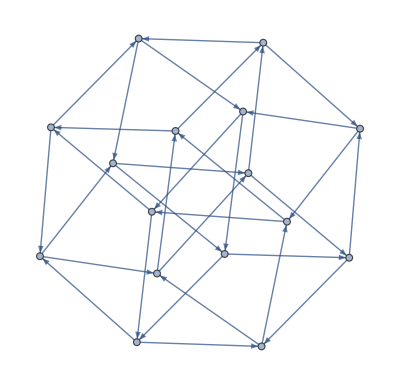

```mathematica
SimpleCayleyGraphBuilder[{PhaseGate[2,1],PhaseGate[2,2]}]
```

#### Undirected Cayley Graphs

To replace pairs of oppositely-directed edges, which connect the same two vertices, with a single undirected edge the UndirectedCayleyGraphBuilder[] function is called.

```mathematica
UndirectedCayleyGraphBuilder[{CNOTGate[2,{1,2}],PhaseGate[2,2]},{{RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824]},{RGBColor[0.05, 0.6900000000000001, 0.027450980392156862]}}]
```

-Graphics-

```mathematica
UndirectedCayleyGraphBuilder[{HadamardGate[1,1],PhaseGate[1,1]},{Directive[RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],Dashed],Directive[RGBColor[0.24720000000000014, 0.24, 0.6],Thick]}]
```

-Graphics-

#### Normalized Cayley Graphs

We incorporate functions to quotient a Cayley graph by an element which acts as a phase on the group. Examples are given with the Clifford group, and Clifford subgroups, where we quotient by (HP)^3.

```mathematica
NormedCayleyGraphBuilder[{HadamardGate[2,1],PhaseGate[2,1]},{{RGBColor[0., 0., 0.]},{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862]}}]
```

-Graphics-

An undirected version of the normed graph is available with the NormedUndirectedCayleyGraphBuilder[] function.

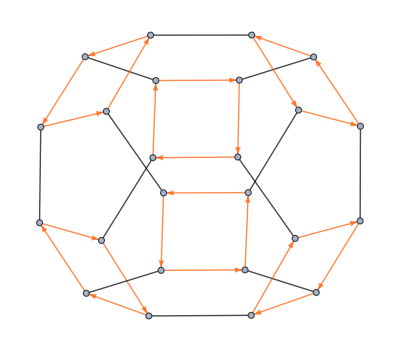

```mathematica
NormedUndirectedCayleyGraphBuilder[{HadamardGate[2,1],PhaseGate[2,1]},{{RGBColor[0., 0., 0.]},{RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862]}}]
```

## Quotienting Cayley Graphs

We can quotient a Cayley graph by the stabilizer subgroup of a chosen state using the CayleyGraphQuotient13[] function (note a version in Mathematica 12 is available with CayleyGraphQuotient12[]). First, the user generates a Cayley graph to quotient. This serves as the first input to the function.  Next a quantum state is chosen, which serves as the second input to the function.

```mathematica
cayleyGraph = CayleyGraphBuilder[{HadamardGate[1,1],PhaseGate[1,1]},{Directive[RGBColor[0.8901960784313725, 0.25, 0],Thick],Directive[RGBColor[0.24720000000000014, 0.63, 0.6],Thick]}]
CayleyGraphQuotient13[cayleyGraph,Transpose[{{1,0}}]]
```

-Graphics-

-Graphics-

```mathematica
cayleyGraph = CayleyGraphBuilder[{PhaseGate[2,1],PhaseGate[2,2],CNOTGate[2,{2,1}]},{Directive[Black,Thick],Directive[Red,Thick],Directive[RGBColor[0.24720000000000014, 0.63, 1],Thick]}]
CayleyGraphQuotient13[cayleyGraph,Transpose[{{1,0,0,1}}]]
```

-Graphics-

-Graphics-